```mathematica
Needs["JLink`"]
ReinstallJava[JVMArguments -> "-Xmx1024m"];
```

```mathematica
SetDirectory["/home/adam/Desktop/Modeling/Data"]
```

/home/adam/Desktop/Modeling/Data

```mathematica
Datastuff= Import["ProblemC56Var.xlsx"];
```

```mathematica
Clear[f]
f[{x_,y_,z_,a_}]:={x,y,IntegerPart[z],a}
```

```mathematica
Clear[ModifiedData]
ModifiedData=Map[f,Datastuff[[1]]];
```

```mathematica
Clear[AZData,TXData,NMData,CAData]
AZData=Cases[ModifiedData,{_,"AZ",_,_}];
TXData=Cases[ModifiedData,{_,"TX",_,_}];
NMData=Cases[ModifiedData,{_,"NM",_,_}];
CAData=Cases[ModifiedData,{_,"CA",_,_}];
```

```mathematica
StateData={AZData,TXData,NMData,CAData};
```

```mathematica
Produced=Drop[Map[First,Datastuff[[2]]],2];
```

```mathematica
Consumed=Flatten@Drop[Drop[Map[Take[#,{4}]&,Datastuff[[2]]],2],-34];
```

```mathematica
Clear[TimeFunc,VarFunc,RemoveState,ProducedVars,ConsumedVars,DataFunc]
VarFunc[{a_,b_,c_,d_}]:={a}
TimeFunc[{a_,b_,c_,d_}]:={c,d}
RemoveState[{a_,b_,c_,d_}]:={a,c,d}
DataFunc[{a_,b_,c_,d_}]:=d
ProducedVars[dataset_]:=Map[Cases[dataset,#]&,Table[{i,_,_,_},{i,Produced}]]
ConsumedVars[dataset_]:=Map[Cases[dataset,#]&,Table[{i,_,_,_},{i,Consumed}]]
```

```mathematica
Clear[AZProduced,TXProduced,NMProduced,CAProduced]
{AZProduced,TXProduced,NMProduced,CAProduced}=Map[ProducedVars,StateData];
```

```mathematica
Clear[AZConsumed,TXConsumed,NMConsumed,CAConsumed]
{AZConsumed,TXConsumed,NMConsumed,CAConsumed}=Map[ConsumedVars,StateData];
```

```mathematica
Clear[TimeRemove]
TimeRemove[dataset_]:=Map[TimeFunc[#]&,dataset]
```

```mathematica
Clear[CalculatingROC,OverlappedLists,Pairs,CROC];
CalculatingROC[{a_,b_}]:=b-a;
CROC[data_]:=Table[CalculatingROC[i],{i,data}];
OverlappedLists[data_]:=Map[Partition[#,2,1]&,data];
Pairs[data_]:=Map[Partition[#,2,1]&,data];
```

```mathematica
{AZPart,TXPart,NMPart,CAPart}=Table[Map[DataFunc,i,{2}],{i,{AZProduced,TXProduced,NMProduced,CAProduced}}];
```

```mathematica
Clear[ModelV2];
ModelV2[dataset_]:=Module[
{data0=dataset},
Clear[AZPart,TXPart,NMPart,CAPart];
{AZPart,TXPart,NMPart,CAPart}=Table[Map[DataFunc,i,{2}],{i,data0}];

LastModelV2[{PyramidalSubtractionAZ,PyramidalSubtractionTX,PyramidalSubtractionNM,PyramidalSubtractionCA}];
Clear[n,lists,PyramidalSubtractionAZ,PyramidalSubtractionTX,PyramidalSubtractionNM,PyramidalSubtractionCA];
n=0;
Print[ProgressIndicator[Dynamic[n],{0,49}]];
lists={};
lists=Append[lists,Table[Map[Last,i],{i,{AZPart,TXPart,NMPart,CAPart}}]];
LastModelV2[{AZPart,TXPart,NMPart,CAPart}];
While[
n<49,
{LastModelV2[{PyramidalSubtractionAZ,PyramidalSubtractionTX,PyramidalSubtractionNM,PyramidalSubtractionCA}]}
;n++];
Return[lists];
]
```

```mathematica
Clear[LastModelV2];
LastModelV2[data_]:=Module[{d=data},
{PyramidalSubtractionAZ,PyramidalSubtractionTX,PyramidalSubtractionNM,PyramidalSubtractionCA}=Map[OverlappedLists,d];
{PyramidalSubtractionAZ,PyramidalSubtractionTX,PyramidalSubtractionNM,PyramidalSubtractionCA}=Map[Table[CROC[i],{i,#}]&,{PyramidalSubtractionAZ,PyramidalSubtractionTX,PyramidalSubtractionNM,PyramidalSubtractionCA}];
lists=Append[lists,Table[Map[Last,i],{i,{PyramidalSubtractionAZ,PyramidalSubtractionTX,PyramidalSubtractionNM,PyramidalSubtractionCA}}]];
];
```

```mathematica
LastModelV2[{AZPart,TXPart,NMPart,CAPart}]
```

Append::normal: Nonatomic expression expected at position 1 in Append[lists,{{-55.2095,-9.28478,0.,-3164.7,0.21764,-149.038,-6.91402,-395.639,-45466.8,«27»,-3.29909,-8676.36,0.,0.,532.082,-90762.4,-4.09191,-342.942,-2.85497},{«1»},«1»,{«1»}}].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Append[lists,{{-55.2095,-9.28478,0.,-3164.7,0.21764,-149.038,-6.91402,-395.639,-45466.8,«27»,-3.29909,-8676.36,0.,0.,532.082,-90762.4,-4.09191,-342.942,-2.85497},{«1»},«1»,{«1»}}].

```mathematica
Clear[TaylorSeriesLastV2]
TaylorSeriesLastV2[x_,{n0_}]:=x*(t-49)^(n0-1)*(1/Factorial[n0])
```

```mathematica
lists=ModelV2[{AZProduced,TXProduced,NMProduced,CAProduced}];
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Append[lists,{{-55.2095,-9.28478,0.,-3164.7,0.21764,-149.038,-6.91402,-395.639,-45466.8,«27»,-3.29909,-8676.36,0.,0.,532.082,-90762.4,-4.09191,-342.942,-2.85497},{«1»},«1»,{«1»}}].

Last::nolast: {} has zero length and no last element.

General::stop: Further output of Last::nolast will be suppressed during this calculation.

```mathematica
Clear[AZSlopes,TXSlopes,NMSlopes,CASlopes]
AZSlopes=Transpose[PadRight[Map[Part[#,1]&,Table[Map[DeleteCases[#,_Last]&,i],{i,Drop[lists,-1]}]]]];
TXSlopes=Transpose[PadRight[Map[Part[#,2]&,Table[Map[DeleteCases[#,_Last]&,i],{i,Drop[lists,-1]}]]]];
NMSlopes=Transpose[PadRight[Map[Part[#,3]&,Table[Map[DeleteCases[#,_Last]&,i],{i,Drop[lists,-1]}]]]];
CASlopes=Transpose[PadRight[Map[Part[#,4]&,Table[Map[DeleteCases[#,_Last]&,i],{i,Drop[lists,-1]}]]]];
```

```mathematica
AZMonomials=Table[MapIndexed[TaylorSeriesLastV2,i],{i,AZSlopes}];
TXMonomials=Table[MapIndexed[TaylorSeriesLastV2,i],{i,TXSlopes}];
NMMonomials=Table[MapIndexed[TaylorSeriesLastV2,i],{i,NMSlopes}];
CAMonomials=Table[MapIndexed[TaylorSeriesLastV2,i],{i,CASlopes}];
```

```mathematica
AZSystemConsumption=Map[Total,AZMonomials];
TXSystemConsumption=Map[Total,TXMonomials];
NMSystemConsumption=Map[Total,NMMonomials];
CASystemConsumption=Map[Total,CAMonomials];
```

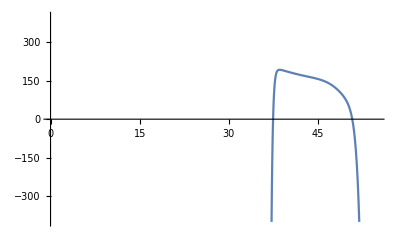

```mathematica
Plot[AZSystemConsumption[[1]],{t,30,55},PlotRange->{{0,55},{-400,400}}]
```

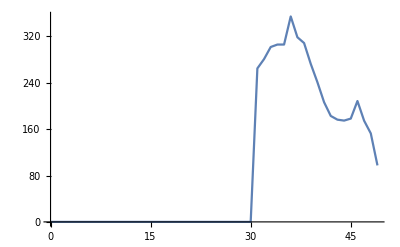

-Graphics-

```mathematica
Clear[LastModel];
LastModel[data_]:=Module[{d=data},
{PyramidalSubtractionAZ,PyramidalSubtractionTX,PyramidalSubtractionNM,PyramidalSubtractionCA}=Map[OverlappedLists,d];
{PyramidalSubtractionAZ,PyramidalSubtractionTX,PyramidalSubtractionNM,PyramidalSubtractionCA}=Map[Table[CROC[i],{i,#}]&,{PyramidalSubtractionAZ,PyramidalSubtractionTX,PyramidalSubtractionNM,PyramidalSubtractionCA}];
lists=Append[lists,Table[Map[Median,i],{i,{PyramidalSubtractionAZ,PyramidalSubtractionTX,PyramidalSubtractionNM,PyramidalSubtractionCA}}]];
];
```

```mathematica
Clear[Model];
Model[dataset_]:=Module[
{data0=dataset},
Clear[AZPart,TXPart,NMPart,CAPart];
{AZPart,TXPart,NMPart,CAPart}=Table[Map[DataFunc,i,{2}],{i,data0}];
{AZPart,TXPart,NMPart,CAPart}=Table[Map[DeleteDuplicates[Chop[#]]&,i],{i,{AZPart,TXPart,NMPart,CAPart}}];

Clear[CalculatingROC,OverlappedLists,Pairs,CROC];
CalculatingROC[{a_,b_}]:=b-a;
CROC[data_]:=Table[CalculatingROC[i],{i,data}];
OverlappedLists[data_]:=Map[Partition[#,2,1]&,data];
Pairs[data_]:=Map[Partition[#,2,1]&,data];

LastModel[{PyramidalSubtractionAZ,PyramidalSubtractionTX,PyramidalSubtractionNM,PyramidalSubtractionCA}];
Clear[n,lists,PyramidalSubtractionAZ,PyramidalSubtractionTX,PyramidalSubtractionNM,PyramidalSubtractionCA];
n=0;
Print[ProgressIndicator[Dynamic[n],{0,49}]];
lists={};
lists=Append[lists,Table[Map[Median,i],{i,{AZPart,TXPart,NMPart,CAPart}}]];
LastModel[{AZPart,TXPart,NMPart,CAPart}];
While[
n<49,
{LastModel[{PyramidalSubtractionAZ,PyramidalSubtractionTX,PyramidalSubtractionNM,PyramidalSubtractionCA}]}
;n++];
Clear[TaylorSeriesLast];
TaylorSeriesLast[x_,{n0_}]:=x*(t-30)^(n0-1)*(1/Factorial[n0]);
Clear[AZSlopes,TXSlopes,NMSlopes,CASlopes];

AZSlopes=Transpose[PadRight[Map[Part[#,1]&,Table[Map[DeleteCases[#,_Median]&,i],{i,Drop[lists,-1]}]]]];

TXSlopes=Transpose[PadRight[Map[Part[#,2]&,Table[Map[DeleteCases[#,_Median]&,i],{i,Drop[lists,-1]}]]]];

NMSlopes=Transpose[PadRight[Map[Part[#,3]&,Table[Map[DeleteCases[#,_Median]&,i],{i,Drop[lists,-1]}]]]];

CASlopes=Transpose[PadRight[Map[Part[#,4]&,Table[Map[DeleteCases[#,_Median]&,i],{i,Drop[lists,-1]}]]]];

AZMonomials=Table[MapIndexed[TaylorSeriesLast,i],{i,AZSlopes}];

TXMonomials=Table[MapIndexed[TaylorSeriesLast,i],{i,TXSlopes}];

NMMonomials=Table[MapIndexed[TaylorSeriesLast,i],{i,NMSlopes}];

CAMonomials=Table[MapIndexed[TaylorSeriesLast,i],{i,CASlopes}];

AZSystemConsumption=Map[Total,AZMonomials];

TXSystemConsumption=Map[Total,TXMonomials];

NMSystemConsumption=Map[Total,NMMonomials];

CASystemConsumption=Map[Total,CAMonomials];

Return[{AZSystemConsumption,TXSystemConsumption,NMSystemConsumption,CASystemConsumption}];
]
```

```mathematica
LastModel[{AZPart,TXPart,NMPart,CAPart}]
```

```mathematica
StateSystem=Model[{AZProduced,TXProduced,NMProduced,CAProduced}];
```

```mathematica
StateSystem[[1]][[1]]
```

224.768-3.20958 (-30+t)+0.752941 (-30+t)^2+0.271045 (-30+t)^3+0.023682 (-30+t)^4+0.00856314 (-30+t)^5-0.0107267 (-30+t)^6+0.000694226 (-30+t)^7-0.000174666 (-30+t)^8-5.94707×10^-6 (-30+t)^9+5.96801×10^-6 (-30+t)^10-7.3505×10^-7 (-30+t)^11-1.11255×10^-7 (-30+t)^12-6.02797×10^-8 (-30+t)^13+1.6235×10^-9 (-30+t)^14-1.02536×10^-9 (-30+t)^15+1.02963×10^-10 (-30+t)^16-3.20495×10^-11 (-30+t)^17+1.89947×10^-12 (-30+t)^18-6.87321×10^-13 (-30+t)^19+6.20003×10^-13 (-30+t)^20+7.81382×10^-14 (-30+t)^21-6.99417×10^-15 (-30+t)^22-7.19258×10^-16 (-30+t)^23+5.89651×10^-17 (-30+t)^24+1.05814×10^-18 (-30+t)^25-2.46993×10^-19 (-30+t)^26-2.46704×10^-20 (-30+t)^27+4.44059×10^-22 (-30+t)^28-9.94858×10^-23 (-30+t)^29+1.21384×10^-24 (-30+t)^30-1.15085×10^-25 (-30+t)^31-1.09674×10^-26 (-30+t)^32-1.68481×10^-28 (-30+t)^33+2.83771×10^-29 (-30+t)^34-3.33282×10^-30 (-30+t)^35-6.26996×10^-32 (-30+t)^36-1.12991×10^-32 (-30+t)^37+1.15488×10^-34 (-30+t)^38-5.65388×10^-35 (-30+t)^39-1.65665×10^-37 (-30+t)^40-1.20865×10^-37 (-30+t)^41-1.99683×10^-39 (-30+t)^42-4.05994×10^-40 (-30+t)^43-5.49049×10^-42 (-30+t)^44-1.23842×10^-42 (-30+t)^45-1.08191×10^-44 (-30+t)^46-3.09052×10^-45 (-30+t)^47-1.81386×10^-47 (-30+t)^48-6.50543×10^-48 (-30+t)^49

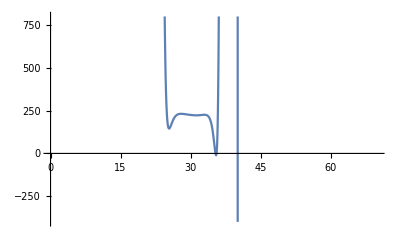

```mathematica
Plot[StateSystem[[1]][[1]],{t,0,70},PlotRange->{{0,70},{-400,800}}]
```

```mathematica
Clear[LastModelFirst];
LastModelFirst[data_]:=Module[{d=data},
{PyramidalSubtractionAZ,PyramidalSubtractionTX,PyramidalSubtractionNM,PyramidalSubtractionCA}=Map[OverlappedLists,d];
{PyramidalSubtractionAZ,PyramidalSubtractionTX,PyramidalSubtractionNM,PyramidalSubtractionCA}=Map[Table[CROC[i],{i,#}]&,{PyramidalSubtractionAZ,PyramidalSubtractionTX,PyramidalSubtractionNM,PyramidalSubtractionCA}];
lists=Append[listsFirst,Table[Map[First,i],{i,{PyramidalSubtractionAZ,PyramidalSubtractionTX,PyramidalSubtractionNM,PyramidalSubtractionCA}}]];
];
```

```mathematica
Clear[ModelFirst];
ModelFirst[dataset_]:=Module[
{data0=dataset},
Clear[AZPart,TXPart,NMPart,CAPart];
{AZPart,TXPart,NMPart,CAPart}=Table[Map[DataFunc,i,{2}],{i,data0}];
{AZPart,TXPart,NMPart,CAPart}=Table[Map[DeleteDuplicates[Chop[#]]&,i],{i,{AZPart,TXPart,NMPart,CAPart}}];

Clear[CalculatingROC,OverlappedLists,Pairs,CROC];
CalculatingROC[{a_,b_}]:=b-a;
CROC[data_]:=Table[CalculatingROC[i],{i,data}];
OverlappedLists[data_]:=Map[Partition[#,2,1]&,data];
Pairs[data_]:=Map[Partition[#,2,1]&,data];

LastModelFirst[{PyramidalSubtractionAZ,PyramidalSubtractionTX,PyramidalSubtractionNM,PyramidalSubtractionCA}];
Clear[n,listsFirst,PyramidalSubtractionAZ,PyramidalSubtractionTX,PyramidalSubtractionNM,PyramidalSubtractionCA];
n=0;
Print[ProgressIndicator[Dynamic[n],{0,49}]];
listsFirst={};
listsFirst=Append[listsFirst,Table[Map[First,i],{i,{AZPart,TXPart,NMPart,CAPart}}]];
LastModelFirst[{AZPart,TXPart,NMPart,CAPart}];
While[
n<49,
{LastModelFirst[{PyramidalSubtractionAZ,PyramidalSubtractionTX,PyramidalSubtractionNM,PyramidalSubtractionCA}],
listsFirst=Append[listsFirst,Table[Map[First,i],{i,{PyramidalSubtractionAZ,PyramidalSubtractionTX,PyramidalSubtractionNM,PyramidalSubtractionCA}}]]}
;n++];
Return[listsFirst];
]
```

```mathematica
LastModelFirst[{AZPart,TXPart,NMPart,CAPart}]
```

Append::normal: Nonatomic expression expected at position 1 in Append[listsFirst,{{264.816,16.3321,1.2888,548.567,0.21824,-1207.17,0.04254,-175.986,«29»,-1098.74,-187.522,0.08489,3527.56,21841.4,0.09583,-175.986,0.06682},«2»,{-32.8722,-«20»,«42»,«21»}}].

```mathematica
Clear[TaylorSeriesFirst]
TaylorSeriesFirst[x_,{n0_}]:=x*(t-20)^(n0-1)*(1/Factorial[n0])
```

```mathematica
listsFirst=ModelFirst[{AZProduced,TXProduced,NMProduced,CAProduced}];
```

Append::normal: Nonatomic expression expected at position 1 in Append[listsFirst,{{-248.745,-7.9181,-0.59762,-1081.95,-0.20848,2660.24,-0.06077,11.1515,6079.22,«28»,549.407,516.078,0.16882,-3372.66,-1726.34,-0.02506,11.1515,-0.02137},«2»,{«1»}}].

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First::nofirst will be suppressed during this calculation.

```mathematica
Clear[AZSlopesFirst,TXSlopesFirst,NMSlopesFirst,CASlopesFirst]
AZSlopesFirst=Transpose[PadRight[Map[Part[#,1]&,Table[Map[DeleteCases[#,_First]&,i],{i,Drop[listsFirst,-1]}]]]];
TXSlopesFirst=Transpose[PadRight[Map[Part[#,2]&,Table[Map[DeleteCases[#,_First]&,i],{i,Drop[listsFirst,-1]}]]]];
NMSlopesFirst=Transpose[PadRight[Map[Part[#,3]&,Table[Map[DeleteCases[#,_First]&,i],{i,Drop[listsFirst,-1]}]]]];
CASlopesFirst=Transpose[PadRight[Map[Part[#,4]&,Table[Map[DeleteCases[#,_First]&,i],{i,Drop[listsFirst,-1]}]]]];
```

```mathematica
AZMonomialsFirst=Table[MapIndexed[TaylorSeriesFirst,i],{i,AZSlopesFirst}];
TXMonomialsFirst=Table[MapIndexed[TaylorSeriesFirst,i],{i,TXSlopesFirst}];
NMMonomialsFirst=Table[MapIndexed[TaylorSeriesFirst,i],{i,NMSlopesFirst}];
CAMonomialsFirst=Table[MapIndexed[TaylorSeriesFirst,i],{i,CASlopesFirst}];
```

```mathematica
AZSystemConsumption=Map[Total,AZMonomialsFirst];
TXSystemConsumption=Map[Total,TXMonomialsFirst];
NMSystemConsumption=Map[Total,NMMonomialsFirst];
CASystemConsumption=Map[Total,CAMonomialsFirst];
```

```mathematica
AZSystemConsumption[[1]]
```

-124.373 (-20+t)+42.2576 (-20+t)^2-11.4584 (-20+t)^3+2.57449 (-20+t)^4-0.420519 (-20+t)^5+0.0141282 (-20+t)^6+0.0201869 (-20+t)^7-0.00877877 (-20+t)^8+0.00234943 (-20+t)^9-0.000484188 (-20+t)^10+0.0000827462 (-20+t)^11-0.0000121806 (-20+t)^12+1.58163×10^-6 (-20+t)^13-1.84126×10^-7 (-20+t)^14+1.9438×10^-8 (-20+t)^15-1.87613×10^-9 (-20+t)^16+1.66681×10^-10 (-20+t)^17-1.37464×10^-11 (-20+t)^18+6.30224×10^-10 (-20+t)^19-6.43493×10^-11 (-20+t)^20+6.14233×10^-12 (-20+t)^21-5.49754×10^-13 (-20+t)^22+4.62316×10^-14 (-20+t)^23-3.65752×10^-15 (-20+t)^24+2.72397×10^-16 (-20+t)^25-1.91027×10^-17 (-20+t)^26+1.26135×10^-18 (-20+t)^27-7.83912×10^-20 (-20+t)^28+4.58232×10^-21 (-20+t)^29-2.51665×10^-22 (-20+t)^30+1.29664×10^-23 (-20+t)^31-6.25483×10^-25 (-20+t)^32+2.81851×10^-26 (-20+t)^33-1.18405×10^-27 (-20+t)^34+4.63872×10^-29 (-20+t)^35-1.70857×10^-30 (-20+t)^36+6.09318×10^-32 (-20+t)^37-2.26155×10^-33 (-20+t)^38+9.72729×10^-35 (-20+t)^39-5.07635×10^-36 (-20+t)^40+2.98207×10^-37 (-20+t)^41-1.78637×10^-38 (-20+t)^42+1.0347×10^-39 (-20+t)^43-5.69675×10^-41 (-20+t)^44+2.97761×10^-42 (-20+t)^45-1.48345×10^-43 (-20+t)^46+7.08036×10^-45 (-20+t)^47-3.25271×10^-46 (-20+t)^48

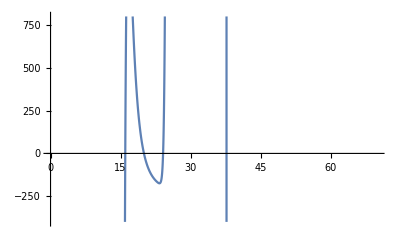

```mathematica
Plot[AZSystemConsumption[[1]],{t,0,70},PlotRange->{{0,70},{-400,800}}]
```